```mathematica
ClearAll["Global`*"]
```

```mathematica
(*This section is supposed to test out how varies transform from Fourier series representation to DFT representation. For details of how we are checking that check the python code "cd Desktop/Books/Codes/Python/PhaseTransition/DFT_Test.py"*)
```

```mathematica
Nn:=21(*Plug in odd values, since we have written the following codes keeping that in mind.*)
(*Array[hk,{Nn},{0}];*)
T:=2
```

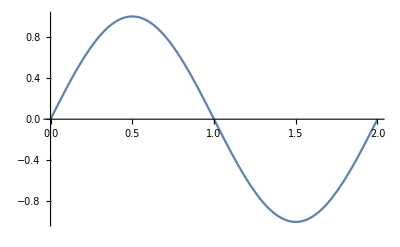

```mathematica
(*h[x_]:=Piecewise[{{(1+x/Pi),-Pi<=x<0},{(1-x/Pi),0<=x<Pi}},0]*)
h[x_]:=Sin[(2*Pi)/T*x]
Plot[h[x],{x,0,T}]
```

```mathematica
hk:=Table[FourierCoefficient[h[x],x,n,FourierParameters->{1,(2*Pi)/T}],{n,Floor[-Nn/2]+1,Floor[Nn/2]}]
DFThk:=RotateRight[hk,Floor[Nn/2]+1](*Used RotateRight to cycle the entries to match better with the DFT output.*)
hk
DFThk
RotateRight[DFThk,Floor[Nn/2]]
{DFThk[[2]],DFThk[[Nn]]}
```

{0,0,0,0,0,0,0,0,0,ⅈ/2,0,-ⅈ/2,0,0,0,0,0,0,0,0,0}

{0,-ⅈ/2,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,ⅈ/2}

{0,0,0,0,0,0,0,0,0,ⅈ/2,0,-ⅈ/2,0,0,0,0,0,0,0,0,0}

{-ⅈ/2,ⅈ/2}

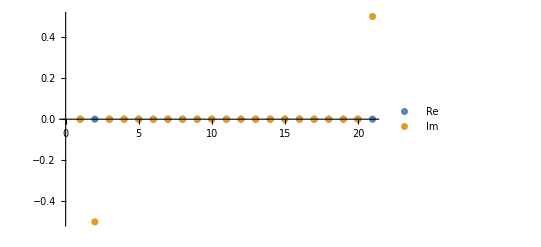

```mathematica
ListPlot[{Re[DFThk],Im[DFThk]},PlotLegends->{"Re","Im"}]
```

```mathematica
A[x_]:=Sum[-I*((2*Pi*ii)/T)*hk[[ii+Floor[Nn/2]+1]]*Exp[I*(2*Pi*ii)/T*x],{ii,Floor[-Nn/2]+1,Floor[Nn/2]}]//Together//FullSimplify
```

```mathematica
Table[-I*((2*Pi*ii)/T)*hk[[ii+Floor[Nn/2]+1]]*Exp[I*(2*Pi*ii)/T*x],{ii,Floor[-Nn/2]+1,Floor[Nn/2]}]
```

{0,0,0,0,0,0,0,0,0,-1/2 ⅇ^(-ⅈ π x) π,0,-1/2 ⅇ^(ⅈ π x) π,0,0,0,0,0,0,0,0,0}

```mathematica
A[x]
```

-π Cos[π x]

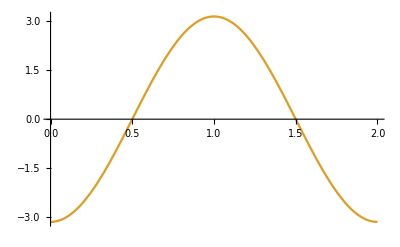

```mathematica
Plot[{A[x],-Pi*Cos[Pi*x]},{x,0,T}](*No idea why this wont plot*)
```

```mathematica
(*PErforming DFT of sin(2π*x/L) manually.*)
Hatf:=Table[h[k*T/Nn],{k,0,Nn-1}]
HatTildef:=Table[Total[Sin[(2*Pi)/Nn*Range[0,Nn-1]].Exp[-2*Pi*I*n*Range[0,Nn-1]/Nn]],{n,0,Nn-1}]
```

{0.,3.96508×10^-18-0.5 ⅈ,-5.28678×10^-18-3.70074×10^-17 ⅈ,2.64339×10^-18+2.11471×10^-17 ⅈ,-1.98254×10^-18+5.28678×10^-18 ⅈ,7.93016×10^-18-1.58603×10^-17 ⅈ,-2.64339×10^-18+0. ⅈ,-6.60847×10^-19+0. ⅈ,-5.28678×10^-18+5.28678×10^-18 ⅈ,0.+0. ⅈ,0.-8.45884×10^-17 ⅈ,0.+8.45884×10^-17 ⅈ,0.+0. ⅈ,5.28678×10^-18-5.28678×10^-18 ⅈ,6.60847×10^-19+0. ⅈ,2.64339×10^-18+0. ⅈ,-7.93016×10^-18+1.58603×10^-17 ⅈ,1.98254×10^-18-5.28678×10^-18 ⅈ,-2.64339×10^-18-2.11471×10^-17 ⅈ,5.28678×10^-18+3.70074×10^-17 ⅈ,-3.96508×10^-18+0.5 ⅈ}

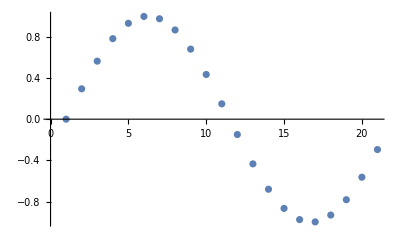

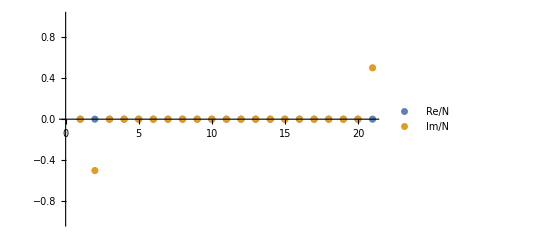

```mathematica
HatTildef/Nn//N
ListPlot[Hatf]
ListPlot[{Re[HatTildef/Nn],Im[HatTildef/Nn]},PlotRange->{-1,1},PlotLegends->{"Re/N","Im/N"}]
```

```mathematica
(*This section is supposed to test out how Python PErforms DFT. We try out simple examples in Python and manually perform the calculation here. This is accesory to the above code. The following calcualtion corresponds to performing the DFT of sin(2*pi*x/L). At the moment of writing this, we were expexting the DFT to be two delta peaks as well of amplitude +/-i/2. But we were getting an amplitude of pi/2.*)
```

```mathematica
(*Computing the DFT of sin(2pi/L*x). Notice that the componets corresponding to n=1 and n=Nt-1 blow up here but not when we compute the DFT using the algorithm laid out before.*)
Manipulate[Table[Sum[Sin[(2*Pi)/2*k*2/Nt]*Exp[-2*Pi*I*k*n/Nt],{k,0,Nt-1}]//N,{n,0,Nt-1,1}],{Nt,1,20,1}]
Manipulate[ListPlot[Table[Sum[Sin[k*(2*Pi)/Nt]*Exp[-2*Pi*I*k*n/Nt],{k,0,Nt-1}],{n,0,Nt-1,1}],PlotRange->{-0.1,10}],{Nt,1,100,1}]
```

Σ|'Their discretization'-'our discretization'|=0.0000232198

Total[Re[DFTN]]=6.88451×10^-15

Im[DFTN]={0,-50.,4.0431×10^-16,-3.50041×10^-7,-7.44181×10^-17,-1.80423×10^-6,-7.52587×10^-17,1.33802×10^-6,-7.16522×10^-17,-4.12734×10^-7,2.00116×10^-17,4.5613×10^-6,1.77965×10^-17,1.30555×10^-8,1.45996×10^-16,3.51141×10^-7,6.79481×10^-17,-1.31648×10^-6,1.5683×10^-16,-2.15015×10^-6,-9.32997×10^-17,-1.63207×10^-6,-3.83355×10^-17,1.77717×10^-7,2.01336×10^-15,-8.×10^-6,-1.95569×10^-15,-7.60296×10^-6,2.53098×10^-16,4.01798×10^-6,1.49529×10^-16,-6.25475×10^-6,1.11459×10^-17,3.70886×10^-6,-2.22252×10^-17,-4.35114×10^-6,-3.44152×10^-17,-3.99094×10^-6,-5.16571×10^-17,-2.7204×10^-6,-5.63486×10^-17,-7.10688×10^-6,-4.74469×10^-17,5.2243×10^-6,9.8149×10^-17,5.80423×10^-6,1.63231×10^-16,-6.24101×10^-7,-8.17016×10^-16,8.10254×10^-7,0,-8.10254×10^-7,8.17016×10^-16,6.24101×10^-7,-1.63231×10^-16,-5.80423×10^-6,-9.8149×10^-17,-5.2243×10^-6,4.74469×10^-17,7.10688×10^-6,5.63486×10^-17,2.7204×10^-6,5.16571×10^-17,3.99094×10^-6,3.44152×10^-17,4.35114×10^-6,2.22252×10^-17,-3.70886×10^-6,-1.11459×10^-17,6.25475×10^-6,-1.49529×10^-16,-4.01798×10^-6,-2.53098×10^-16,7.60296×10^-6,1.95569×10^-15,8.×10^-6,-2.01336×10^-15,-1.77717×10^-7,3.83355×10^-17,1.63207×10^-6,9.32997×10^-17,2.15015×10^-6,-1.5683×10^-16,1.31648×10^-6,-6.79481×10^-17,-3.51141×10^-7,-1.45996×10^-16,-1.30555×10^-8,-1.77965×10^-17,-4.5613×10^-6,-2.00116×10^-17,4.12734×10^-7,7.16522×10^-17,-1.33802×10^-6,7.52587×10^-17,1.80423×10^-6,7.44181×10^-17,3.50041×10^-7,-4.0431×10^-16,50.}

Total[Abs[Im[DFTN]]]=100.

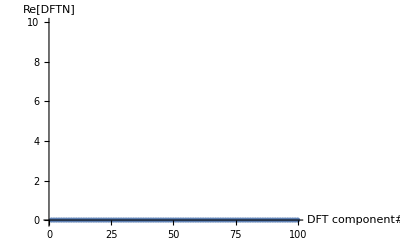

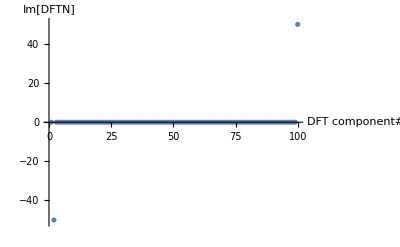

6.88451×10^-15+0. ⅈ

Σ|'What our code computes'-'FL1'| =0.000153632

kΔx-xprime=   {0.,0.29831,0.59662,0.89493,1.19324,1.49155,1.78986,2.08817,2.38648,2.68479,2.9831,3.28141,3.57972,3.87803,4.17634,4.47465,4.77296,5.07127,5.36958,5.66789,5.9662,6.26451,6.56282,6.86113,7.15944,7.45775,7.75606,8.05437,8.35268,8.65099,8.9493,9.24761,9.54592,9.84423,10.1425,10.4408,10.7392,11.0375,11.3358,11.6341,11.9324,12.2307,12.529,12.8273,13.1256,13.4239,13.7223,14.0206,14.3189,14.6172,14.9155,15.2138,15.5121,15.8104,16.1087,16.407,16.7054,17.0037,17.302,17.6003,17.8986,18.1969,18.4952,18.7935,19.0918,19.3901,19.6885,19.9868,20.2851,20.5834,20.8817,21.18,21.4783,21.7766,22.0749,22.3732,22.6716,22.9699,23.2682,23.5665,23.8648,24.1631,24.4614,24.7597,25.058,25.3563,25.6547,25.953,26.2513,26.5496,26.8479,27.1462,27.4445,27.7428,28.0411,28.3394,28.6377,28.9361,29.2344,29.5327}

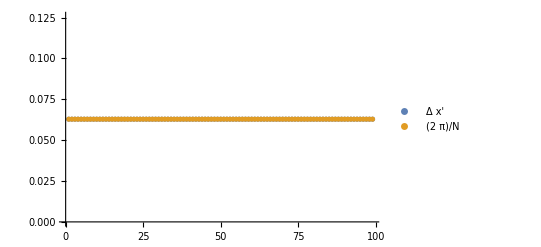

Σ|Δ(xprime)*π-(2*π)/N|=  2.5896×10^-14

```mathematica
(*For Ngrid=100 in the code, L1 contains the array of values sin(x)at the discretization chosen. FL1 is the DFT of that array.*)
Clear[L1,FL1,DFTN,xprime,Temp1,Temp2,Temp3]
L1:={0.000000,0.062791,0.125333,0.187381,0.248690,0.309017,0.368125,0.425779,0.481754,0.535827,0.587785,0.637424,0.684547,0.728969,0.770513,0.809017,0.844328,0.876307,0.904827,0.929776,0.951057,0.968583,0.982287,0.992115,0.998027,1.000000,0.998027,0.992115,0.982287,0.968583,0.951057,0.929776,0.904827,0.876307,0.844328,0.809017,0.770513,0.728969,0.684547,0.637424,0.587785,0.535827,0.481754,0.425779,0.368125,0.309017,0.248690,0.187381,0.125333,0.062791,0.000000,-0.062791,-0.125333,-0.187381,-0.248690,-0.309017,-0.368125,-0.425779,-0.481754,-0.535827,-0.587785,-0.637424,-0.684547,-0.728969,-0.770513,-0.809017,-0.844328,-0.876307,-0.904827,-0.929776,-0.951057,-0.968583,-0.982287,-0.992115,-0.998027,-1.000000,-0.998027,-0.992115,-0.982287,-0.968583,-0.951057,-0.929776,-0.904827,-0.876307,-0.844328,-0.809017,-0.770513,-0.728969,-0.684547,-0.637424,-0.587785,-0.535827,-0.481754,-0.425779,-0.368125,-0.309017,-0.248690,-0.187381,-0.125333,-0.062791}
Temp1:=Total[Abs[L1-Table[Sin[k*(2*Pi)/Length[L1]],{k,0,Length[L1]-1}]]](*This is comparing the discrete value of sin(x) with our choice of discretization, there is an error*)
Print["Σ|'Their discretization'-'our discretization'|=",Temp1]
FL1:={-0.00000000+0.00000000I,-0.00000000-50.00000000I,-0.00000000+0.00000000I,0.00000000-0.00000000I,-0.00000000+0.00000000I, 0.00000000-0.00000000I,-0.00000000+0.00000000I,-0.00000000-0.00000000I,-0.00000000-0.00000000I,-0.00000000-0.00000000I, 0.00000000-0.00000000I,-0.00000000+0.00000000I,0.00000000-0.00000000I,0.00000000+0.00000000I, 0.00000000-0.00000000I,-0.00000000+0.00000000I, 0.00000000+0.00000000I, 0.00000000+0.00000000I,-0.00000000+0.00000000I, 0.00000000-0.00000000I,-0.00000000+0.00000000I,-0.00000000-0.00000000I,-0.00000000+0.00000000I, 0.00000000-0.00000000I,0.00000000-0.00000000I,-0.00000000+0.00000000I, 0.00000000-0.00000000I,0.00000000-0.00000000I, 0.00000000-0.00000000I, 0.00000000-0.00000000I,0.00000000+0.00000000I,-0.00000000-0.00000000I,-0.00000000-0.00000000I,0.00000000+0.00000000I,0.00000000+0.00000000I, 0.00000000+0.00000000I,-0.00000000-0.00000000I,-0.00000000+0.00000000I,-0.00000000+0.00000000I,-0.00000000+0.00000000I, 0.00000000-0.00000000I,0.00000000-0.00000000I,-0.00000000+0.00000000I,-0.00000000+0.00000000I,-0.00000000-0.00000000I,0.00000000-0.00000000I, 0.00000000+0.00000000I,-0.00000000+0.00000000I,-0.00000000+0.00000000I,-0.00000000+0.00000000I,-0.00000000+0.00000000I,-0.00000000+0.00000000I,-0.00000000-0.00000000I,-0.00000000-0.00000000I,0.00000000-0.00000000I,0.00000000+0.00000000I,-0.00000000+0.00000000I,-0.00000000-0.00000000I,-0.00000000-0.00000000I, 0.00000000+0.00000000I,0.00000000+0.00000000I,-0.00000000-0.00000000I,-0.00000000-0.00000000I,-0.00000000-0.00000000I,-0.00000000+0.00000000I, 0.00000000-0.00000000I,0.00000000-0.00000000I, 0.00000000-0.00000000I,-0.00000000+0.00000000I,-0.00000000+0.00000000I, 0.00000000-0.00000000I, 0.00000000+0.00000000I,0.00000000+0.00000000I, 0.00000000+0.00000000I, 0.00000000+0.00000000I,-0.00000000-0.00000000I,0.00000000+0.00000000I, 0.00000000+0.00000000I,-0.00000000-0.00000000I,-0.00000000+0.00000000I,-0.00000000-0.00000000I,0.00000000+0.00000000I,-0.00000000-0.00000000I, 0.00000000-0.00000000I,0.00000000-0.00000000I,-0.00000000-0.00000000I, 0.00000000+0.00000000I,0.00000000-0.00000000I, 0.00000000+0.00000000I,-0.00000000-0.00000000I,0.00000000+0.00000000I,-0.00000000+0.00000000I,-0.00000000+0.00000000I,-0.00000000+0.00000000I,-0.00000000-0.00000000I, 0.00000000+0.00000000I,-0.00000000-0.00000000I, 0.00000000+0.00000000I,-0.00000000-0.00000000I,-0.00000000+50.00000000I}
DFTN:=Table[Total[L1.Exp[-2*Pi*I*k*Range[0,Length[L1]-1]/Length[L1]]],{k,0,Length[L1]-1}]
Print["Total[Re[DFTN]]=",Total[Re[DFTN]]]
Print["Im[DFTN]=",Im[DFTN]]
Print["Total[Abs[Im[DFTN]]]=",Total[Abs[Im[DFTN]]]]
ListPlot[Re[DFTN],PlotRange->{-0.1,10},AxesLabel->{"DFT component#","Re[DFTN]"}](*,{k,0,Length[L1]-1},PlotRange->{-2,2}*)
ListPlot[Im[DFTN],PlotRange->{-51,51},AxesLabel->{"DFT component#","Im[DFTN]"}](*,{k,0,Length[L1]-1},PlotRange->{-40,40}*)
Total[Table[Total[L1.Exp[-2*Pi*I*k*Range[0,Length[L1]-1]/Length[L1]]],{k,0,Length[L1]-1}]-FL1](*Here we run the DFT algorithm and compare to the output of the code, ie, FL1.*)
Print["Σ|'What our code computes'-'FL1'| =",Total[Abs[Table[Total[L1.Exp[-2*Pi*I*k*Range[0,Length[L1]-1]/Length[L1]]],{k,0,Length[L1]-1}]-FL1]]]
(*For Ngrid=100, The discrete values at which the function is being evaluated. We have k*2*pi/N, which didn't seem to match the corresponding v laues in the code; these have been copied over and stores in uprime.*)
xprime:={0.,0.02,0.04,0.06,0.08,0.1,0.12,0.14,0.16,0.18,0.2,0.22,0.24,0.26,0.28,0.3,0.32,0.34,0.36,0.38,0.4,0.42,0.44,0.46,0.48,0.5,0.52,0.54,0.56,0.58,0.6,0.62,0.64,0.66,0.68,0.7,0.72,0.74,0.76,0.78,0.8,0.82,0.84,0.86,0.88,0.9,0.92,0.94,0.96,0.98,1.,1.02,1.04,1.06,1.08,1.1,1.12,1.14,1.16,1.18,1.2,1.22,1.24,1.26,1.28,1.3,1.32,1.34,1.36,1.38,1.4,1.42,1.44,1.46,1.48,1.5,1.52,1.54,1.56,1.58,1.6,1.62,1.64,1.66,1.68,1.7,1.72,1.74,1.76,1.78,1.8,1.82,1.84,1.86,1.88,1.9,1.92,1.94,1.96,1.98}
Temp2:=Table[2/(2*Pi)*k,{k,0,Length[xprime]-1}]-xprime//N(*Checking if xprime = kΔx=kT/N where T is the period and N is the discretization no.*)
Print["kΔx-xprime=   ",Temp2]
ListPlot[{Differences[xprime*Pi],Table[(2*Pi)/Length[xprime],{k,1,Length[Differences[xprime]]}]},PlotLegends->{"Δ x'","(2  π)/N"}]
Temp3:=Total[Abs[Differences[xprime*Pi]-Table[(2*Pi)/Length[xprime],{k,1,Length[Differences[xprime]]}]]]
Print["Σ|Δ(xprime)*π-(2*π)/N|=  ",Temp3]
```

```mathematica
Exp[(2*Pi*I)/T*Range[-10,10,1]]*(-(2*Pi*I)/T*Range[-10,10,1])//N
```

{0.+31.4159 ⅈ,0.-28.2743 ⅈ,0.+25.1327 ⅈ,0.-21.9911 ⅈ,0.+18.8496 ⅈ,0.-15.708 ⅈ,0.+12.5664 ⅈ,0.-9.42478 ⅈ,0.+6.28319 ⅈ,0.-3.14159 ⅈ,0.,0.+3.14159 ⅈ,0.-6.28319 ⅈ,0.+9.42478 ⅈ,0.-12.5664 ⅈ,0.+15.708 ⅈ,0.-18.8496 ⅈ,0.+21.9911 ⅈ,0.-25.1327 ⅈ,0.+28.2743 ⅈ,0.-31.4159 ⅈ}